```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\shiyi\work\git\work\factorial_cumulant\fRG-QM

```mathematica
chi2QMB=Flatten[Import["./mub0_fluc/final/buffer/mu_deriv/chi2.dat"]];
chi4QMB=Flatten[Import["./mub0_fluc/final/buffer/mu_deriv/chi4.dat"]];
R42QMB=chi4QMB/chi2QMB;
chi2QMP=Flatten[Import["./mub0_fluc/final/buffer/muP_deriv/chi2.dat"]];
chi4QMP=Flatten[Import["./mub0_fluc/final/buffer/muP_deriv/chi4.dat"]];
R42QMP=chi4QMP/chi2QMP;
chi2QMPb=Flatten[Import["./mub0_fluc/final/buffer/muPb_deriv/chi2.dat"]];
chi4QMPb=Flatten[Import["./mub0_fluc/final/buffer/muPb_deriv/chi4.dat"]];
R42QMPb=chi4QMPb/chi2QMPb;
chi2PQMB=Flatten[Import["./mub0PQM_fluc/final/buffer/mu_deriv/chi2.dat"]];
chi4PQMB=Flatten[Import["./mub0PQM_fluc/final/buffer/mu_deriv/chi4.dat"]];
R42PQMB=chi4PQMB/chi2PQMB;
chi2PQMP=Flatten[Import["./mub0PQM_fluc/final/buffer/chi2.dat"]];
chi4PQMP=Flatten[Import["./mub0PQM_fluc/final/buffer/chi4.dat"]];
R42PQMP=chi4PQMP/chi2PQMP;
chi2PQMPb=Flatten[Import["./mub0PQM_fluc/final/buffer/muPb_deriv/chi2.dat"]];
chi4PQMPb=Flatten[Import["./mub0PQM_fluc/final/buffer/muPb_deriv/chi4.dat"]];
R42PQMPb=chi4PQMPb/chi2PQMPb;
```

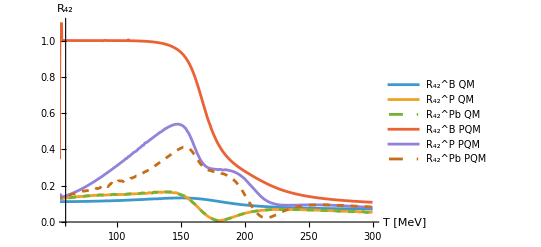

```mathematica
Plot1=ListLinePlot[{R42QMB,R42QMP,R42QMPb,R42PQMB,R42PQMP,R42PQMPb},PlotStyle->{Automatic,Automatic,Dashed,Automatic,Automatic,Dashed},PlotLegends->{"R_42^B QM","R_42^P QM","R_42^Pb QM","R_42^B PQM","R_42^P PQM","R_42^Pb PQM"},PlotRange->{{60,300},{0,1.1}},AxesLabel->{"T [MeV]","R_42"}]
```

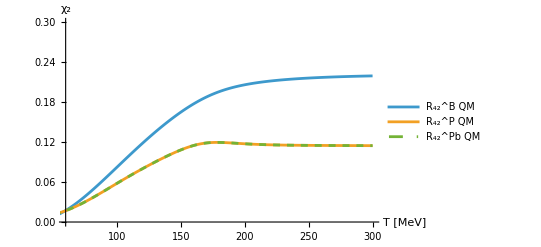

```mathematica
Plot1=ListLinePlot[{chi2QMB,chi2QMP,chi2QMPb(*,R42PQMB,R42PQMP,R42PQMPb*)},PlotStyle->{Automatic,Automatic,Dashed,Automatic,Automatic,Dashed},PlotLegends->{"R_42^B QM","R_42^P QM","R_42^Pb QM"(*,"χ_2 PQM","χ_2^P PQM","χ_2^Pb PQM"*)},PlotRange->{{60,300},{0,0.3}},AxesLabel->{"T [MeV]","χ_2"}]
```

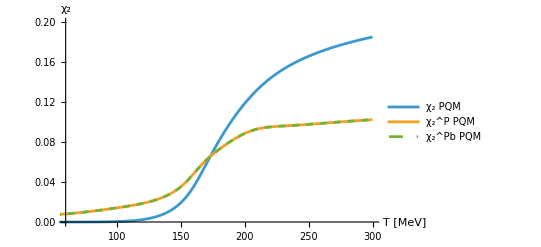

```mathematica
Plot1=ListLinePlot[{(*chi2QMB,chi2QMP,chi2QMPb,*)chi2PQMB,chi2PQMP,chi2PQMPb},PlotStyle->{Automatic,Automatic,Dashed,Automatic,Automatic,Dashed},PlotLegends->{(*"R_42^B QM","R_42^P QM","R_42^Pb QM",*)"χ_2 PQM","χ_2^P PQM","χ_2^Pb PQM"},PlotRange->{{60,300},{0,0.2}},AxesLabel->{"T [MeV]","χ_2"}]
```

```mathematica
Export["R42.pdf",Plot1]
```

R42.pdf